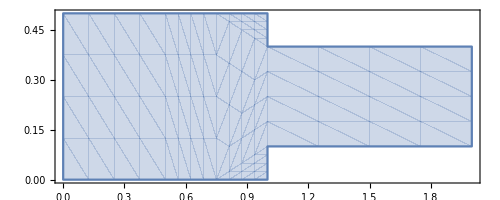

```mathematica
(*Start of given code*)
Ω=RegionUnion[Rectangle[{0,0},{1,1/2}],Rectangle[{1,1/10},{2,2/5}]];
plotΩ=RegionPlot[Ω,AspectRatio->Automatic]
```

```mathematica
op={({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}/.μ->1;
pde=op=={0,0,0};
bcs={
DirichletCondition[u[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<x<2],
DirichletCondition[p[x,y]==0.,x== 2]};
{xVel,yVel,pressure}=NDSolveValue[{op=={0,0,0},bcs},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.0005}}];
(*End of given code*)
```

```mathematica
(*The velocity of the fluid*)
Show[plotΩ,VectorPlot[{xVel[x,y], yVel[x,y]},{x,y}∈Ω,PlotLabel->"Velocity of the fluid in Ω"]]

(*The pressure of the fluid*)
Plot3D[pressure[x,y],{x,y}∈Ω,PlotLabel->"Pressure of the fluid in Ω"]
Show[plotΩ,ContourPlot[pressure[x,y],{x,y}∈Ω,PlotLabel->"Pressure of the fluid in Ω"]]
```

```mathematica
minT=0;
maxT=10;
leftOmega = Parallelepiped[{0,0,0},{{1,0,0},{0,0.5,0},{0,0,maxT}}];
rightOmega = Parallelepiped[{1,0.1,0},{{1,0,0},{0,0.3,0},{0,0,maxT}}];
(*Show[Graphics3D[leftOmega],Graphics3D[rightOmega]]*)
omegaWithT = RegionUnion[leftOmega,rightOmega];
```

```mathematica
d=1;
Γ=Rectangle[{0,0.1},{0.3,0.5}];
Subscript[c, 0]=1;
u0[x,y] :=If[{x,y}∈Γ,Subscript[c, 0],0] 
Clear[u];
Clear[conc];
conc = NDSolveValue[{
D[u[x,y,t], t]-d ∇_{x,y}^2 u[x,y,t]+{xVel,yVel}.∇_{x,y} u[x,y,t]==NeumannValue[0,True],
u[x,y,0]==u0[x,y]},
u,
{x,y,t}∈omegaWithT];
Manipulate[
ContourPlot[conc[x,y,t],
{x,0,0.5},{y,0,2},Contours->15],
{t,minT,maxT}
]
```

DiscretizeGraphics::rnimpl: The function DiscretizeGraphics is not implemented for Tetrahedron[«1»].

NDSolveValue::nmesh: A mesh could not be generated from Tetrahedron[{{{1.,0.5,9.375},{0.5,0.5,9.0625},{1.,0.4,9.375},{0.5,0.5,10.}},{{1.,0.1,1.25},{0.5,0.,0.9375},{1.,0.,1.25},{0.5,0.,1.5625}},«47»,{{1.,0.5,1.25},{0.5,0.5,0.9375},{1.,0.4,1.25},{0.5,0.5,1.5625}},«302»}].

NDSolveValue[{u^(0,0,1)[x,y,t]+InterpolatingFunction[…] u^(0,1,0)[x,y,t]-u^(0,2,0)[x,y,t]+InterpolatingFunction[…] u^(1,0,0)[x,y,t]-u^(2,0,0)[x,y,t]==NeumannValue[0,True],u[x,y,0]==If[{x,y}∈Rectangle[1,1],c_0,0]},u,{x,y,t}∈1]
 |  |  |  |

DiscretizeGraphics::rnimpl: The function DiscretizeGraphics is not implemented for Tetrahedron[«1»].

NDSolveValue::nmesh: A mesh could not be generated from Tetrahedron[{{{1.,0.5,9.375},{0.5,0.5,9.0625},{1.,0.4,9.375},{0.5,0.5,10.}},{{1.,0.1,1.25},{0.5,0.,0.9375},{1.,0.,1.25},{0.5,0.,1.5625}},«47»,{{1.,0.5,1.25},{0.5,0.5,0.9375},{1.,0.4,1.25},{0.5,0.5,1.5625}},«302»}].

NDSolveValue::dsvar: 0.0000357143 cannot be used as a variable.

NDSolveValue::dsvar: 0.03575 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

```mathematica
d=1;
circleCenter = {10,10};
R=10;
r=1;
minT=0;
maxT=20;
Ω=Disk[circleCenter, R];
NonZeroΩ=Disk[circleCenter, r];
omegaWithT = Cylinder[{Append[circleCenter,minT],Append[circleCenter,maxT]},R];
(*Ensure no transit between Ω and the rest of the plane*)
bondaryCondition = {NeumannValue[0,True]};
u0[x,y]:=If[{x,y}∈NonZeroΩ,1,0]
Clear[uSol];
Clear[u];
uSol = NDSolveValue[{
D[u[x,y,t], t]-d ∇_{x,y}^2 u[x,y,t]==NeumannValue[0,True],
u[x,y,0]==u0[x,y]},
u,
{x,y,t}∈omegaWithT
];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
badGrad =  -{D[uSol[xx,yy,tt],xx],D[uSol[xx,yy,tt],yy]};
gradU[x_,y_,t_] :=badGrad/.{xx->x,yy->y,tt->t}
Manipulate[
Show[
{ContourPlot[uSol[x,y,t],
{x,0,20},{y,0,20},Contours->15
(*{x,y}∈Ω*)],
(*VectorPlot[∇_{x,y} uSol[x,y,t],{x,0,20},{y,0,20}]*)
VectorPlot[gradU[x,y,t],{x,0,20},{y,0,20},VectorStyle->Red]
}],
{t,minT,maxT}
]
```

{InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t],InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t]}

InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t]

InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][1,y,t]

```mathematica
uf = u[x,y]
ut = uf/.{x->r Cos[θ], y-> r Sin[θ]}
Simplify[1/r D[(r  D[ut, r]), r] + 1/r^2 D[ut, θ,θ]] == (D[uf, x,x] + D[uf, y,y])/.{x->r Cos[θ], y-> r Sin[θ]}
```

u[x,y]

u[r Cos[θ],r Sin[θ]]

True